# PH20 ASSIGNMENT 6

## Question 1

```mathematica
Clear[v,θ,g,u,ux,uy];
x[v_,θ_,t_]:=ReplaceAll[Subscript[t, a]->t][v Cos[θ] Subscript[t, a]]
y[v_,θ_,t_]:=ReplaceAll[Subscript[t, a]->t][v Sin[θ] Subscript[t, a]-(g Subscript[t, a]^2)/2]
{t0,tf}=Values[Solve[y[v,θ,t]==0,t]];
range = x[v,θ,tf];
optimal= FullSimplify[Solve[{D[range,θ]==0,0≤θ≤π/2},θ]]
θ = π/4;
distance = 850; (* distance from Caltech to PCC *)
g = 9.80665;

u=Solve[{range==distance,v≥0},v][[1]];
ux=v Cos[θ]/.u
uy = v Sin[θ] /.u
utotal = v /. u
```

{{θ→π/4}}

64.5587

64.5587

91.2998

## Question 2

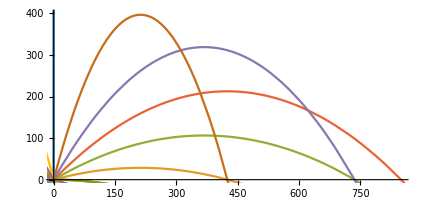

```mathematica
(* In this plot, the red line represents the 45 degree agle *)
ParametricPlot[Evaluate[Table[{x[utotal,θ,t],y[utotal,θ,t]},{θ,0,2 Pi,Pi/12}]],{t,0,200},PlotRange->{{0,850},{0,400}}]
```

## Question 3

```mathematica
mass = 0.5;
radius = 0.05;
density = 1.3;

Clear[θ, v];
vel = Sqrt[x'[t]^2 + y'[t]^2];

differential = ParametricNDSolve[{x''[t]+(density * radius^2* vel)/(2 * mass) x'[t]==0,
y''[t]+g+(density * radius^2* vel)/(2 * mass) y'[t]==0,x'[0]==v Cos[θ],y'[0]==v Sin[θ],x[0]==0,y[0]==0},{x,y},{t,0,30},{v,θ}];
θ = Pi/4;
v = 91.29979463284678 ;

ParametricPlot[{Evaluate[x[v,θ][t]/.differential],Evaluate[y[v,θ][t]/.differential]},{t,0,20}, PlotRange->{{0,850},{0,400}}]
(* Major decrease in range with drag which makes sense *)
```

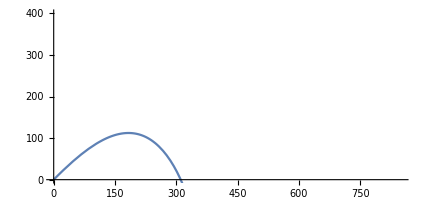

## Question 4

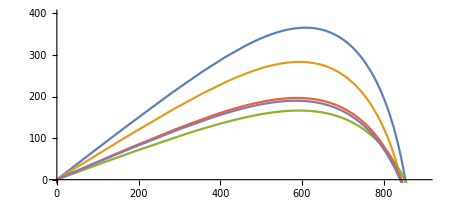

```mathematica
ParametricPlot[{{Evaluate[x[550, 0.65][t] /. differential] ,Evaluate[ y[550, 0.65][t] /. differential]}, {Evaluate[x[485, 0.55][t] /. differential] ,Evaluate[ y[485, 0.55][t] /. differential]},{Evaluate[x[500, 0.35][t] /. differential] ,Evaluate[ y[500, 0.35][t] /. differential]},{Evaluate[x[475, 0.41][t] /. differential] ,Evaluate[ y[475, 0.41][t] /. differential]},{Evaluate[x[472, 0.4][t] /. differential] ,Evaluate[ y[472, 0.4][t] /. differential]}}, {t,0,30} , PlotRange->{{0,900},{0,400}}]

(* From the above plot we can observe tjat tje angle of 0.4 gives the same range as the others, but with the lowest possible velocity *)
```

## Question 5

```mathematica
clear[v];

landingTime[v_ , θ_] := FindRoot[y[v,θ][t]/.differential,{t,20}][[1]]

range2[v_, θ_] := x[v,θ][t/.landingTime[v,θ]]/.differential

findVelocity[ra_,θ_]:= Module[{v=0,range=0},
							While[range2[v,θ]<ra,v+=5];
							While[range2[v,θ]>ra,v-=1];
							While[range2[v,θ]<ra,v+=0.1];
							While[range2[v,θ]>ra,v-= 0.5];
							While[range2[v,θ]<ra,v+=0.01];
							v
							]

FindAngle[ra_]:=Module[{θ=0.1,v1=0.1,v2=0},
					While[v2<v1,
						{v2=findVelocity[ra,(θ+0.01)],
						v1=findVelocity[ra,θ],
						θ += 0.01}];

					While[v2<v1,
						{v2=findVelocity[ra,(θ-0.001)],
						v1=findVelocity[ra,θ],
						θ -= 0.001}];

					While[v2<v1,
						{v2=findVelocity[ra,(θ+0.0001)],
						v1=findVelocity[ra,θ],
						θ += 0.0001}];

					θ
					]
FindAngle[850]
```

```mathematica
0.4600000000000003

(* This shows that numerically the angle of 0.46 radians is the optimal angle when we include drag *)
```